### Problem 1

{0,0,-u_0}

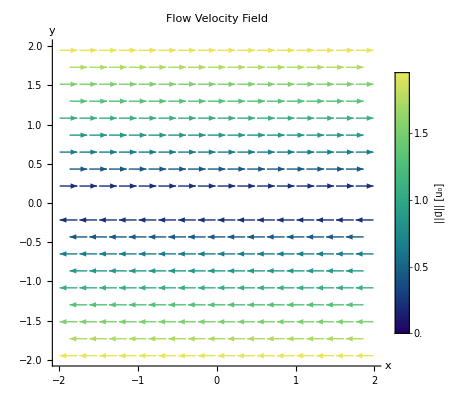

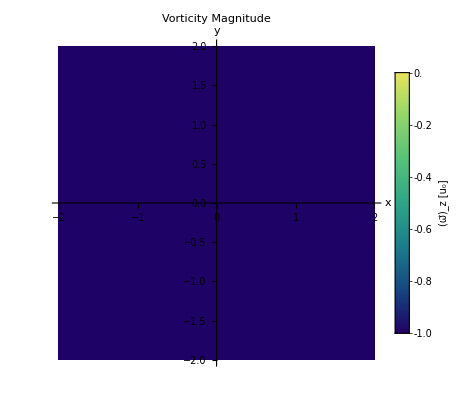

```mathematica
u[x_,y_,z_]={Subscript[u, 0] y,0,0};
ω[x_,y_,z_]=∇_{x,y,z} ×u[x,y,z]
VectorPlot[u[x,y,0][[1;;2]]/.Subscript[u, 0]->1,
{x,-2,2},{y,-2,2},
VectorColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"||u⃗|| [u_0]"],
PlotLabel->"Flow Velocity Field",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
DensityPlot[ω[x,y,0][[3]]/.{Subscript[u, 0]->1},
{x,-2,2},{y,-2,2},
ColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"(ω⃗)_z [u_0]"],
PlotLabel->"Vorticity Magnitude",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
```

### Problem 2

{0,0,2 y u_0}

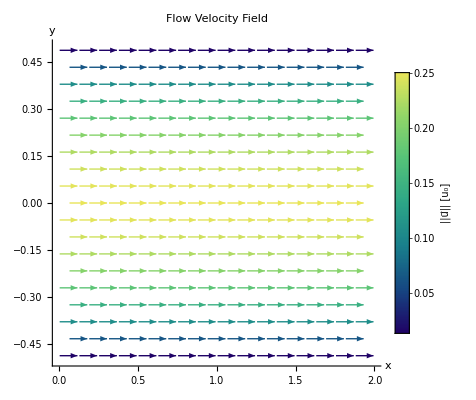

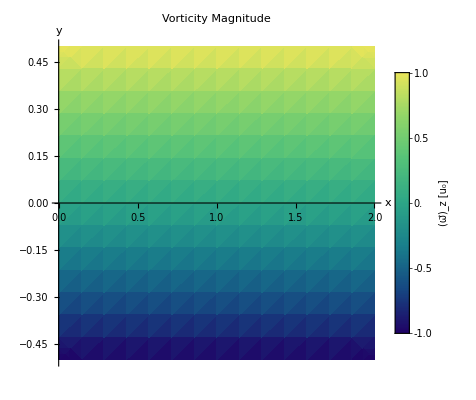

```mathematica
u[x_,y_,z_]={Subscript[u, 0] ((h/2)^2-y^2),0,0};
ω[x_,y_,z_]=∇_{x,y,z} ×u[x,y,z]
VectorPlot[u[x,y,0][[1;;2]]/.{Subscript[u, 0]->1,h->1},
{x,0,2},{y,-1/2,1/2},
VectorColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"||u⃗|| [u_0]"],
PlotLabel->"Flow Velocity Field",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
DensityPlot[ω[x,y,0][[3]]/.{Subscript[u, 0]->1},
{x,0,2},{y,-1/2,1/2},
ColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"(ω⃗)_z [u_0]"],
PlotLabel->"Vorticity Magnitude",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
```

### Problem 3

{0,0,2 Ω}

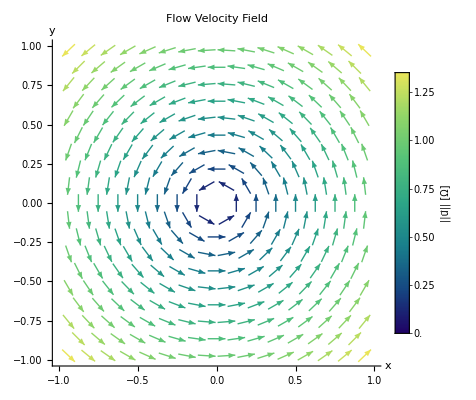

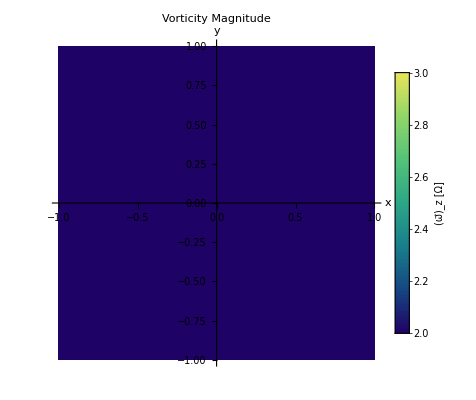

```mathematica
u[x_,y_,z_]=Ω Norm[{x,y}]Normalize[{-y,x,0}];
ω[x_,y_,z_]=Assuming[x∈Reals&&y∈Reals&&z∈Reals,∇_{x,y,z} ×u[x,y,z]//FullSimplify]
VectorPlot[u[x,y,0][[1;;2]]/.{Ω->1},
{x,-1,1},{y,-1,1},
VectorColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"||u⃗|| [Ω]"],
PlotLabel->"Flow Velocity Field",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
DensityPlot[ω[x,y,0][[3]]/.{Ω->1},
{x,-1,1},{y,-1,1},
ColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"(ω⃗)_z [Ω]"],
PlotLabel->"Vorticity Magnitude",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
```

### Problem 4

{0,0,0}

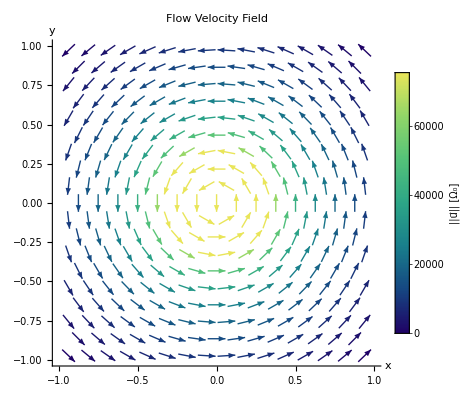

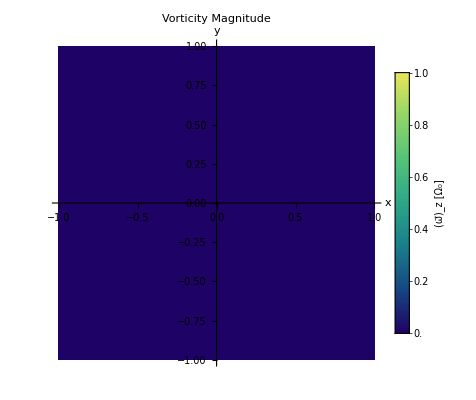

```mathematica
u[x_,y_,z_]=Subscript[Ω, 0]/Norm[{x,y}] Normalize[{-y,x,0}];
ω[x_,y_,z_]=Assuming[x∈Reals&&y∈Reals&&z∈Reals,∇_{x,y,z} ×u[x,y,z]//FullSimplify]
VectorPlot[u[x,y,0][[1;;2]]/.{Subscript[Ω, 0]->1},
{x,-1,1},{y,-1,1},
VectorColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"||u⃗|| [Ω_0]"],
PlotLabel->"Flow Velocity Field",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
DensityPlot[ω[x,y,0][[3]]/.{Subscript[Ω, 0]->1},
{x,-1,1},{y,-1,1},
ColorFunction->"BlueGreenYellow",
PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"(ω⃗)_z [Ω_0]"],
PlotLabel->"Vorticity Magnitude",
Frame->False,
Axes->True,
AxesLabel->{x,y}]
```